```mathematica
data = Import["C:\\Users\\Jesus Enrique\\Documents\\bookanalysis.csv"];
```

```mathematica
byWeight=Table[{data[[i,1]],data[[i,2]]},{i,1,Length[data]}];
byStdev=Table[{data[[i,1]],data[[i,3]]},{i,1,Length[data]}];
byStdevweight=Table[{data[[i,1]],data[[i,2]]*data[[i,3]]},{i,1,Length[data]}];
```

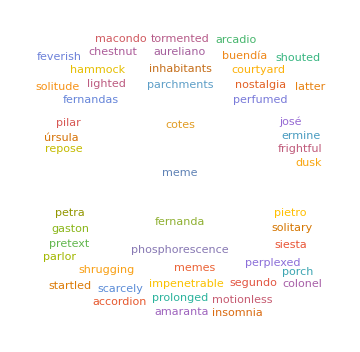

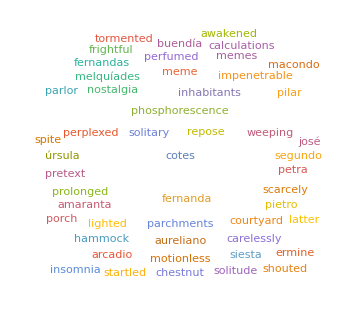

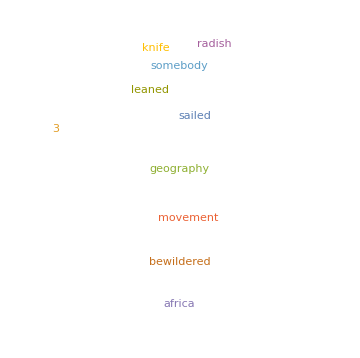

```mathematica
WordCloud[byWeight, MaxItems->50, ImageSize->Medium]
WordCloud[byStdevweight, MaxItems->50, ImageSize->Medium]
WordCloud[byStdev, MaxItems->10, ImageSize->Medium]
```

0.000328407

0.000328407

{{meme,5465.47},{cotes,21665.7},{fernanda,8764.81},{memes,2537.94},{phosphorescence,8158.46},{inhabitants,5355.18},{parchments,2126.77},{pietro,1955.91},{aureliano,3407.82},{petra,1853.73},{siesta,3202.67},{shrugging,0.0765189},2287,{positions,0.},{maneuvering,0.},{speed,0.},{weather,0.},{beach,0.},{bom,0.},{drifted,0.},{fishing,0.},{anymore,0.},{ruined,0.},{schools,0.},{steady,0.}}
 |  |  |  |

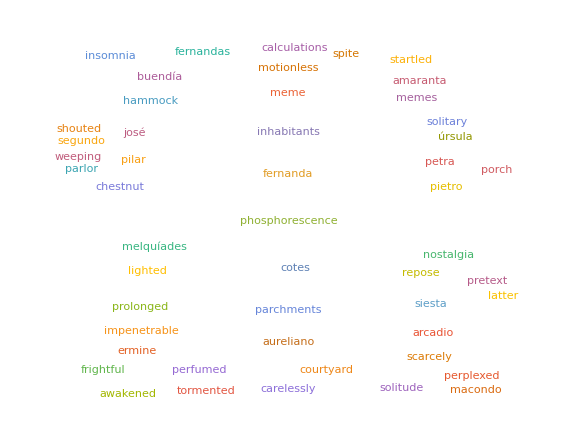

```mathematica
k1 = 1./Max[data[[;;,2]]]
k2 = k1
byParams = Table[{data[[i,1]],data[[i,2]] *(k1 + k2 data[[i,3]])},{i,1,Length[data]}]
WordCloud[byParams, MaxItems->50, ScalingFunctions->Log,ImageSize->Large]
```

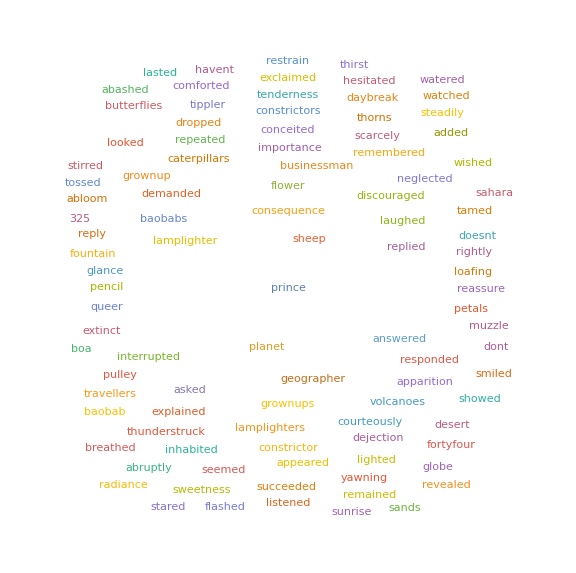

```mathematica
WordCloud[data, MaxItems->100,ImageSize->Large]
```